### Initializations

```mathematica
Exit[]
```

```mathematica
SetDirectory[NotebookDirectory[]];
path=SetDirectory[NotebookDirectory[]];
```

NotebookDirectory::nosv: The notebook 2di5s_shm is not saved.

SetDirectory::badfile: The specified argument $Failed should be a valid string or File.

NotebookDirectory::nosv: The notebook 2di5s_shm is not saved.

SetDirectory::badfile: The specified argument $Failed should be a valid string or File.

```mathematica
{C1,C2,C3,C4,C5,C6,C7,C8,C9,C10,C11,C12,C13}={RGBColor["#195c92"],RGBColor["#d11141"],RGBColor["#009E60"],RGBColor["#FFA500"],
RGBColor["#34DCE3"],RGBColor["#DC00E3"],RGBColor["#8FDE44"],RGBColor["#4FB6E3"],
RGBColor["#E05BE0"],RGBColor["#1370DE"],RGBColor["#B52E66"],RGBColor["#FA6705"],RGBColor["#319F8F"]}

Integerise[x_]:=If[Round[x]==x,ToString[Round@x]<>".0",ToString@x]

leg[label_,dim_,α_,x_,y_,col_]:=Inset[Rotate[Style[label,dim,col,FontFamily->"CMU Serif",Italic],α Degree],Scaled[{x,y}]]

rules[size_]:={size,FontFamily->"CMU Serif",Italic};
```

{RGBColor[0.09803921568627451, 0.3607843137254902, 0.5725490196078431],RGBColor[0.8196078431372549, 0.06666666666666667, 0.2549019607843137],RGBColor[0., 0.6196078431372549, 0.3764705882352941],RGBColor[1., 0.6470588235294118, 0.],RGBColor[0.20392156862745098, 0.8627450980392157, 0.8901960784313725],RGBColor[0.8627450980392157, 0., 0.8901960784313725],RGBColor[0.5607843137254902, 0.8705882352941177, 0.26666666666666666],RGBColor[0.30980392156862746, 0.7137254901960784, 0.8901960784313725],RGBColor[0.8784313725490196, 0.3568627450980392, 0.8784313725490196],RGBColor[0.07450980392156863, 0.4392156862745098, 0.8705882352941177],RGBColor[0.7098039215686275, 0.1803921568627451, 0.4],RGBColor[0.9803921568627451, 0.403921568627451, 0.0196078431372549],RGBColor[0.19215686274509805, 0.6235294117647059, 0.5607843137254902]}

### Constants

```mathematica
{pc,msun,cc,G}= {3.085677*10^13,1.4768,299792,6.67*10^-11}; (* in km, km, km/s, and m^3/kg s^2 *)
```

### LISA PSD

In this section, we initialize the PSD of LISA derived from two sources. Maselli uses a previous version of the PSD for his calculations in their 2020 paper https://doi.org/10.1051/0004-6361/202037654 (hereby named `LISA[f_]`). Robson et al. (https://doi.org/10.1088/1361-6382/ab1101) provided the most recent analytical approximation to the LISA PSD in 2019. We included it here for a 4-year mission.

```mathematica
LISA[f_]:=1.0666666666666666*^-18 (1+1654.744283244525 f^2) (8.899*^-23+(9/1000000000000000000000000000000+3.2399999999999996*^-28 
(59049/(100000000000000000000000000000000000000000000000000 f^10)+1/(100000000 f^2)))/(4 f^4 π^4));
```

```mathematica
RobsonLISA[f_]:=5.333333333333333*^-19(1+1646.416301f^2)((1.5*^-11)^2(1+1.6*^-11/f^4)+(((3*^-15)^2(1+1.6*^-7/f^2)(1+f^4/4.096*^-9))/(4π^4f^4)))+(9*^-45f^(-7/3)Exp[-f^(0.138)-221f Sin[521f]](1+Tanh[1680(0.00113-f)]))
```

```mathematica
TraditionalForm[1.0666666666666666*^-18 (1+1654.744283244525 f^2) (8.899*^-23+(9/1000000000000000000000000000000+3.2399999999999996*^-28 
(59049/(100000000000000000000000000000000000000000000000000 f^10)+1/(100000000 f^2)))/(4 f^4 π^4))]
```

1.06667×10^-18 (1654.74 f^2+1) ((3.24×10^-28 (59049/(100000000000000000000000000000000000000000000000000 f^10)+1/(100000000 f^2))+9/1000000000000000000000000000000)/(4 π^4 f^4)+8.899×10^-23)

```mathematica
TraditionalForm[5.333333333333333*^-19(1+1646.416301f^2)((1.5*^-11)^2(1+1.6*^-11/f^4)+(((3*^-15)^2(1+1.6*^-7/f^2)(1+f^4/4.096*^-9))/(4π^4f^4)))+(9*^-45f^(-7/3)Exp[-f^(0.138)-221f Sin[521f]](1+Tanh[1680(0.00113-f)]))]
```

(9 ⅇ^(-f^0.138-221 f sin(521 f)) (tanh(1680 (0.00113-f))+1))/(1000000000000000000000000000000000000000000000 f^(7/3))+5.33333×10^-19 (1646.42 f^2+1) (2.25×10^-22 ((1.6×10^-11)/f^4+1)+(9 ((1.6×10^-7)/f^2+1) (2.44141×10^8 f^4+1))/(4000000000000000000000000000000 π^4 f^4))

We then plot the characteristic amplitude density h_n(f) for both cases to see if they match. From the plot, it seems they diverge for low frequencies which is the regime of higher mass EMRIs and SMBHs. We continue to use Maselli’s PSD since Robson’s PSD was subject to underflows when used for calculating overlaps.

```mathematica
LISASnf=Table[ RobsonLISA[f],{f,10^-5,1,10^-5}];
```

```mathematica
LISAhnf=Table[Sqrt[f RobsonLISA[f]],{f,10^-5,1,10^-5}];
```

```mathematica
Masellisahnf=Table[Sqrt[f LISA[f]],{f,10^-5,1,10^-5}];
```

```mathematica
ticks=Table[{i,10^-5 i},{i,1,10^5}];
```

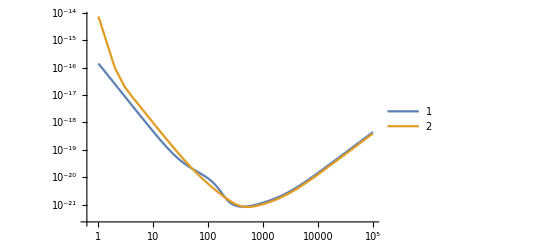

```mathematica
ListLogLogPlot[{LISAhnf,Masellisahnf},Joined->True,PlotLegends->Automatic, Frame->True,FrameTicks->{Automatic,{ticks,None}}]
```

### IMR coefficients

This section provides the analytical form of the IMRPhenomB coefficients derived from Ajith et. al (2011) (https://doi.org/10.1103/PhysRevLett.106.241101).

```mathematica
𝓍={{{-920.9,492.1,135},{6742,-1053,0},{-1.34*10^4,0,0}},
{{1.702 10^4,-9566,-2182},{-1.214*10^5,2.075 10^4,0},{2.386 10^5,0,0}},
{{-1.254*10^5,7.507 10^4,1.338 10^4},{8.735 10^5,-1.657*10^5,0},{-1.694*10^6,0,0}},
{{0,0,0},{0,0,0},{0,0,0}},
{{-8.898*10^5,6.31 10^5,5.068 10^4},{5.981 10^6,-1.415*10^6,0},{-1.128*10^7,0,0}},
{{8.696*10^5,-6.71*10^5,-3.008*10^4},{-5.838*10^6,1.514*10^6,0},{1.089*10^7,0,0}}};

ψ0[χ_]:={3715/756,-16π+113/3 χ,15293365/508032-405/8 χ^2,0,0,0};

𝓎={{{0.6437,0.827,-0.2706},     {-0.05822,-3.935,0},{-7.092,0,0}},
{{0.1469,-0.1228,-0.02609},{-0.0249,0.1701,0},   {2.325,0,0}},
{{-0.4098,-0.03523,0.1008},{1.829,-0.02017,0},   {-2.87,0,0}},
{{-0.1331,-0.08172,0.1451},{-0.2714,0.1279,0},   {4.922,0,0}}};

μ0[χ_]:={1-4.455(1-χ)^0.217+3.521(1-χ)^0.26,(1-0.63(1-χ)^0.3)/2,((1-0.63(1-χ)^0.3) (1-χ)^0.45)/4,0.3236+0.04894χ+0.01346χ^2};

α[η_,χ_]:={-(323/224)+451/168 η,(27/8-11/6 η)χ}; (* α2 and α3 *)

ϵ[χ_]:={1.4547χ-1.8897,-1.8153χ+1.6557}; (* ϵ1 and ϵ2 *)

ψ[k_,η_,χ_]:=ψ0[χ][[k]]+Sum[𝓍[[k,i,j+1]]η^i χ^j,{i,1,3},{j,0,Min[3-i,2]}];

Ψ[f_,M_,η_,χ_,tc_,ϕc_]:=2π f tc+ϕc+3/(128 η (π M f)^(5/3)) (1+Sum[(π M f)^(l/3) ψ[l-1,η,χ],{l,2,7}]);

Ψnew[f_,M_,η_,χ_,tc_,ϕc_]:={3/(128 η (π M f)^(5/3)),3/(128 η (π M f)^(5/3))(π M f)^(2/3) ψ[1,η,χ],3/(128 η (π M f)^(5/3))(π M f)^(3/3) ψ[2,η,χ],3/(128 η (π M f)^(5/3))(π M f)^(4/3) ψ[3,η,χ],3/(128 η (π M f)^(5/3))(π M f)^(5/3) ψ[4,η,χ]+ϕc,3/(128 η (π M f)^(5/3))(π M f)^(6/3) ψ[5,η,χ],3/(128 η (π M f)^(5/3))(π M f)^(7/3) ψ[6,η,χ],2π f tc };

PNfree[phi0_,phi2_,phi3_,phi4_,phi5_,phi6_,phi7_,phi8_]={phi0,phi2,phi3,phi4,phi5,phi6,phi7,phi8};

μ[k_,η_,χ_]:=μ0[χ][[k]]+Sum[𝓎[[k,i,j+1]]η^i χ^j,{i,1,3},{j,0,Min[3-i,2]}];

𝒻1[M_,η_,χ_]:=μ[1,η,χ]/(M π);
𝒻2[M_,η_,χ_]:=μ[2,η,χ]/(M π);
𝒻3[M_,η_,χ_]:=μ[4,η,χ]/(M π);
σLor[M_,η_,χ_] :=μ[3,η,χ]/(M π);
```

```mathematica
PNfree[1,2,3,4,5,6,7,8][[3]]
```

3

```mathematica
D[PNfree[a,b,c,d,e,f,g][[1]],a]
```

1

```mathematica
𝒜i[f_,M_,η_,χ_]:=(f/𝒻1[M,η,χ])^(-7/6) (*(1+Sum[α[η,χ][[i-1]](π M f)^(i/3),{i,2,3}])*);

𝒜m[f_,M_,η_,χ_]:=(f/𝒻1[M,η,χ])^(-2/3) (*(1+Sum[ϵ[χ][[i]](π M f)^(i/3),{i,1,2}])*);

𝒜r[f_,M_,η_,χ_]:=1/(2π) σLor[M,η,χ]/((f-𝒻2[M,η,χ])^2+σLor[M,η,χ]^2/4);

wm[M_,η_,χ_]:=𝒜i[𝒻1[M,η,χ],M,η,χ]/𝒜m[𝒻1[M,η,χ],M,η,χ];

wr[M_,η_,χ_]:=wm[M,η,χ] 𝒜m[𝒻2[M,η,χ],M,η,χ]/𝒜r[𝒻2[M,η,χ],M,η,χ];
```

### Waveform template and dephasing

This section provides the waveform template constructed from the coefficients provided earlier.

#### Phase initializations

We initialize the dephasing factor using the Parametrized Post-Einsteinian form (incorporating the various effects as an exponent of the characteristic velocity), linear in the density of the surrounding medium and complete with the leading PN phase factor.

```mathematica
ϕenv[f_,ℳ_,ρ0_,index_]:=3/(128 (π ℳ f)^(5/3))(π ℳ f)^index*ρ0    (* index = -gamma in Cardoso and Maselli's paper *)
```

Next, we initialize the additional factors coming from Cardoso and Maselli’s Table 1.

```mathematica
kβdrag[m1_,m2_]=-η^-3(1-3η)π^(-11/3)//.η->(m1 m2)/(m1+m2)^2;
kβaccretion[m1_,m2_]=-η^-1 π^-3//.η->(m1 m2)/(m1+m2)^2;
```

The next four cells initialize some ψ_Dthat is added to the phase. (Maybe related to the detector?)

```mathematica
tpp[ν_]:={1,0,4/3(743/336+11/4 η)η^(-2/5),-(32π)/5 η^(-3/5),2(3058673/1016064+5429/1008 η+617/144 η^2)η^(-4/5),((13π)/3 η-(7729π)/252)η^-1};
tf=τ0-5/256 ℳ(π ℳ f)^(-8/3)Sum[tpp[ν][[i]](ℳ π f)^((i-1)/3),{i,1,4}];
ϕT=(2π)/T tf;
```

```mathematica
yr=3600*24*365*299792; (* in km *)
day=3600*24 299792; (* in km *)
RUA=1.495978707 10^8; (* in km *)
RE=6371; (* in km *)
T=1yr;
TE=1day;
```

```mathematica
ϕs=π/2;
θs=0;
{δ,eps}={39.,23.4}π/180;
ϕE=2π tf(1/TE-1/T);
θsT=ArcCos[Cos[θs](Cos[δ]Cos[eps]-Sin[δ]Sin[eps]Cos[ϕE])+Sin[θs](Cos[ϕs](Cos[δ]Cos[eps]+Sin[δ]Cos[eps]Cos[ϕE])-Sin[ϕs]Cos[δ]Sin[ϕE])];
```

```mathematica
ψD[ℳ_,η_,τ0_,f_]=2π f (RUA Sin[θs] Cos[ϕT-ϕs]+RE Cos[θsT]);
```

#### Waveform construction and plots

We then construct `hPhBppE`, or the IMRPhenomB strain e^(i (ψ_D-ψ_env-ψ_PN)) in parametrized Post-Einsteinian form (without the Newtonian amplitude from Berti et. al (2005) https://doi.org/10.1103/PhysRevD.71.084025)

```mathematica
hPhBppE[f_][ℳ_,η_,χ_,tc_,ϕc_,d_,ρ0_,index_]:=With[{M=η^(-3/5)ℳ},Exp[-I (ϕenv[f,ℳ,ρ0,index]+Ψ[f,M,η,χ,tc,ϕc])]]Exp[I ψD[ℳ,η,tc,f]]
```

```mathematica
hPhBppEnew[f_][ℳ_,η_,χ_,tc_,ϕc_,d_,ρ0_,index_]:=With[{M=η^(-3/5)ℳ},Exp[-I (ϕenv[f,ℳ,ρ0,index]+Sum[Ψnew[f,M,η,χ,tc,ϕc][[k]],{k,1,8}])]]Exp[I ψD[ℳ,η,tc,f]]
```

```mathematica
hPhBppEvacnew[f_][ℳ_,η_,tc_,phi0_,phi2_,phi3_,phi4_,phi5_,phi6_,phi7_,phi8_]:=With[{M=η^(-3/5)ℳ},Exp[-I (Sum[(π M f)^(k/3)PNfree[phi0,phi2,phi3,phi4,phi5,phi6,phi7,phi8],{k,1,8}])]]Exp[I ψD[ℳ,η,tc,f]]
```

```mathematica
hPhBppEVac[f_][ℳ_,η_,χ_,tc_,ϕc_,d_]:=With[{M=η^(-3/5)ℳ},Exp[-I (Ψ[f,M,η,χ,tc,ϕc])]]Exp[I ψD[ℳ,η,tc,f]]
```

```mathematica
hPhBppEpull[f_][ℳ_,η_,χ_,tc_,ϕc_,d_,ρ0_,γ_]:=With[{M=η^(-3/5)ℳ},Exp[-I (Ψ[f,M,η,χ,tc,ϕc]+(3/(128 (π ℳ f)^(5/3)) (M)^2 ((M) f)^-γ ρ0  G/cc^2))]]Exp[I ψD[ℳ,η,tc,f]];
hPhBppEdrag[f_][ℳ_,η_,χ_,tc_,ϕc_,d_,ρ0_,γ_]:=With[{M=η^(-3/5)ℳ},Exp[-I (Ψ[f,M,η,χ,tc,ϕc]+(3/(128 (π ℳ f)^(5/3)) (M)^2 ((M) f)^-γ ρ0 G/cc^2(-η^-3(1-3η)π^(-11/3))))]]Exp[I ψD[ℳ,η,tc,f]];
hPhBppEcolless[f_][ℳ_,η_,χ_,tc_,ϕc_,d_,ρ0_,γ_]:=With[{M=η^(-3/5)ℳ},Exp[-I (Ψ[f,M,η,χ,tc,ϕc]+(3/(128 (π ℳ f)^(5/3)) (M)^2 ((M) f)^-γ ρ0 G/cc^2(-η^-1 π^-3)))]]Exp[I ψD[ℳ,η,tc,f]];
```

We also construct the derivative function that consists of derivatives for the six source parameters listed by Cardoso and Maselli. This will be used for calculating the Fisher matrix elements.
THIS TIME AROUND, WE DIFFERENTIATE WITH RESPECT TO THE POST-NEWTONIAN PARAMETERS Φ(f, M, η, χ, Subscript[t, c],ϕ_c).

```mathematica
dhdθ[f_,index_]= {ℳ D[hPhBppE[f][ℳ,η,χ,τ ,ϕ,d,ρ0,index],ℳ],
	 η D[hPhBppE[f][ℳ,η,χ,τ ,ϕ,d,ρ0,index],η],
	   D[hPhBppE[f][ℳ,η,χ,τ ,ϕ,d,ρ0,index],τ],
	   D[hPhBppE[f][ℳ,η,χ,τ ,ϕ,d,ρ0,index],ϕ],
	   D[hPhBppE[f][ℳ,η,χ,τ ,ϕ,d,ρ0,index],χ],
       D[hPhBppE[f][ℳ,η,χ,τ ,ϕ,d,ρ0,index],ρ0]};
```

```mathematica
DhDphi[f_,index_,k_]={
```

The next two plots are checks for order of magnitude of the waveform and its derivative with respect to the surrounding density for an EMRI of central mass 10^5 M_sun and secondary mass of 10 M_sun.

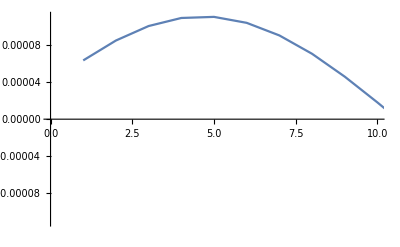

```mathematica
ListLinePlot[{Re[Table[With[{ℳ=398.099msun,η=0.00009998000299960005,χ=0.7999700029997,τ=0 ,ϕ=-Pi/4,d=1000,ρ0=p,index=-2,f=10^-5,C=Sqrt[5]},Evaluate[C (2/5)/(d 10^6 pc π^(2/3))(5/24)^(1/2) (f/cc)^(-7/6) ℳ^(5/6)dhdθ[f,index][[-1]]]],{p,0,1000,1}]]},PlotRange->{{0,10},Automatic}]
```

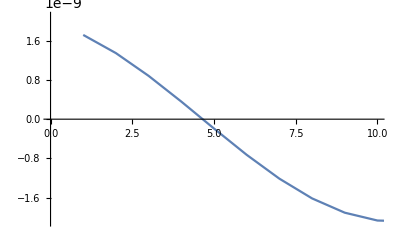

```mathematica
ListLinePlot[Re[Table[With[{ℳ=398.099msun,η=0.00009998000299960005,χ=0.7999700029997,τ=0 ,ϕ=-Pi/4,d=1000,ρ0=p,index=-2, C=Sqrt[5],f=10^-5},Evaluate[C (2/5)/(d 10^6 pc π^(2/3))(5/24)^(1/2) (f/cc)^(-7/6) ℳ^(5/6)hPhBppE[f][ℳ,η,χ,τ,ϕ,d,ρ0,index]]],{p,0,1000,1}]],PlotRange->{{0,10},Automatic}]
```

We then visualize the waveforms in the frequency domain (including the amplitude) from their frequency 4 years before the merger up to ISCO for m_1= 10^5 M_sun, m_2 = 10 M_sun, χ_1=0.8, and χ_2=0.5. We create the vacuum waveform, as well as the dephased waveforms due to gravitational pull, gravitational drag, and collisionless accretion, for a surrounding density of 10^3 kg/m^3.

```mathematica
hptildefd=Re[Table[Evaluate[With[{χ=0.7999700029997,ℳ=398.0992088877798msun,η=0.00009998000299960005,τ=0,ϕ=-π/4,d=10^3}, Sqrt[5](2/5)/(d 10^6 pc π^(2/3))(5/24)^(1/2) (f/cc)^(-7/6) ℳ^(5/6) (hPhBppEVac[f/cc][ℳ,η,χ,τ ,ϕ,d])]],{f,0.00328985,0.113325,10^-5}]];
hpgravfd=Re[Table[Evaluate[With[{χ=0.7999700029997,ℳ=398.0992088877798msun,η=0.00009998000299960005,τ=0,ϕ=-π/4,d=10^3,ρ0=10^3,γ=2}, Sqrt[5](2/5)/(d 10^6 pc π^(2/3))(5/24)^(1/2) (f/cc)^(-7/6) ℳ^(5/6) (hPhBppEpull[f/cc][ℳ,η,χ,τ ,ϕ,d,ρ0,γ])]],{f,0.00328985,0.113325,10^-5}]];
hpdragfd=Re[Table[Evaluate[With[{χ=0.7999700029997,ℳ=398.0992088877798msun,η=0.00009998000299960005,τ=0,ϕ=-π/4,d=10^3,ρ0=10^3,γ=11/3}, Sqrt[5](2/5)/(d 10^6 pc π^(2/3))(5/24)^(1/2) (f/cc)^(-7/6) ℳ^(5/6) (hPhBppEdrag[f/cc][ℳ,η,χ,τ ,ϕ,d,ρ0,γ])]],{f,0.00328985,0.113325,10^-5}]];
hpcollessfd=Re[Table[Evaluate[With[{χ=0.7999700029997,ℳ=398.0992088877798msun,η=0.00009998000299960005,τ=0,ϕ=-π/4,d=10^3,ρ0=10^3,γ=3}, Sqrt[5](2/5)/(d 10^6 pc π^(2/3))(5/24)^(1/2) (f/cc)^(-7/6) ℳ^(5/6) (hPhBppEcolless[f/cc][ℳ,η,χ,τ ,ϕ,d,ρ0,γ])]],{f,0.00328985,0.113325,10^-5}]];
```

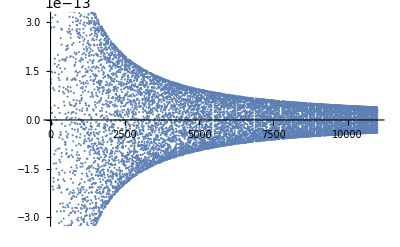

```mathematica
ListPlot[hptildefd]
```

```mathematica
ClearAll[hptildefd,hpcollessfd,hpdragfd,hpgravfd]
```

```mathematica
hptildefd[f_]:=With[{χ=0.7999700029997,ℳ=398.0992088877798msun,η=0.00009998000299960005,τ=0,ϕ=-π/4,d=10^3}, Sqrt[5](2/5)/(d 10^6 pc π^(2/3))(5/24)^(1/2) (f/cc)^(-7/6) ℳ^(5/6) (hPhBppEVac[f/cc][ℳ,η,χ,τ ,ϕ,d])];
hpgravfd[f_]:=With[{χ=0.7999700029997,ℳ=398.0992088877798msun,η=0.00009998000299960005,τ=0,ϕ=-π/4,d=10^3,ρ0=10^3,γ=2}, Sqrt[5](2/5)/(d 10^6 pc π^(2/3))(5/24)^(1/2) (f/cc)^(-7/6) ℳ^(5/6) (hPhBppEpull[f/cc][ℳ,η,χ,τ ,ϕ,d,ρ0,γ])];
hpdragfd[f_]:=With[{χ=0.7999700029997,ℳ=398.0992088877798msun,η=0.00009998000299960005,τ=0,ϕ=-π/4,d=10^3,ρ0=10^3,γ=11/3}, Sqrt[5](2/5)/(d 10^6 pc π^(2/3))(5/24)^(1/2) (f/cc)^(-7/6) ℳ^(5/6) (hPhBppEdrag[f/cc][ℳ,η,χ,τ ,ϕ,d,ρ0,γ])];
hpcollessfd[f_]:=With[{χ=0.7999700029997,ℳ=398.0992088877798msun,η=0.00009998000299960005,τ=0,ϕ=-π/4,d=10^3,ρ0=10^3,γ=3}, Sqrt[5](2/5)/(d 10^6 pc π^(2/3))(5/24)^(1/2) (f/cc)^(-7/6) ℳ^(5/6) (hPhBppEcolless[f/cc][ℳ,η,χ,τ ,ϕ,d,ρ0,γ])] ;(* in units of km^-1 *)
```

```mathematica
Normalize[hptildefd[f],𝒪[LISA[f],hptildefd[f],hptildefd[f],10^-5,1]&]
hptildefd[f]
```

(5.76505×10^-19 ⅇ^(-ⅈ ((113.198 (1.+6.51617 f^(2/3)-29.929 f-14.2584 f^(4/3)-84.3278 f^2+86.7419 f^(7/3)))/f^(5/3)-π/4)+(ⅈ f π (0.+6371 (0.713229-0.249933 Cos[(0.00217763 (1+3.94553 f^(2/3)-31.1189 f))/f^(8/3)])))/149896))/f^(7/6)

(3.07273×10^-15 ⅇ^(-ⅈ ((113.198 (1.+6.51617 f^(2/3)-29.929 f-14.2584 f^(4/3)-84.3278 f^2+86.7419 f^(7/3)))/f^(5/3)-π/4)+(ⅈ f π (0.+6371 (0.713229-0.249933 Cos[(0.00217763 (1+3.94553 f^(2/3)-31.1189 f))/f^(8/3)])))/149896))/f^(7/6)

```mathematica
Re[hpcollessfd[10^-5]]
```

1.29414×10^-9

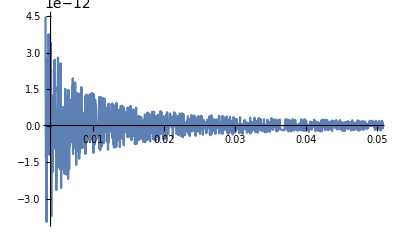

```mathematica
Plot[Re[hptildefd[f]]-Re[hpdragfd[f]],{f,0.00328985,0.113325},PlotRange->{{0.004,0.05},Full}]
```

We also create their corresponding characteristic strain h_c(f) in the frequency domain, for plotting with the noise characteristic amplitude h_n(f) (See Moore et. al (2015). https://doi.org/10.1088/0264-9381/32/1/015014 for the summary of the different waveform conventions)

```mathematica
hcfd=Re[Table[Evaluate[With[{χ=0.7999700029997,ℳ=398.0992088877798msun,η=0.00009998000299960005,τ=0,ϕ=-π/4,d=10^3}, 2 f/cc Sqrt[5](2/5)/(d 10^6 pc π^(2/3))(5/24)^(1/2) (f/cc)^(-7/6) ℳ^(5/6) (hPhBppEVac[f/cc][ℳ,η,χ,τ ,ϕ,d])]],{f,0.0032898520426597314,0.11332458708398821,10^-5}]];
hcgravfd=Re[Table[Evaluate[With[{χ=0.7999700029997,ℳ=398.0992088877798msun,η=0.00009998000299960005,τ=0,ϕ=-π/4,d=10^3,ρ0=10^3,γ=2}, 2 f/cc Sqrt[5](2/5)/(d 10^6 pc π^(2/3))(5/24)^(1/2) (f/cc)^(-7/6) ℳ^(5/6) (hPhBppEpull[f/cc][ℳ,η,χ,τ ,ϕ,d,ρ0,γ])]],{f,0.0032898520426597314,0.11332458708398821,10^-5}]];
hcdragfd=Re[Table[Evaluate[With[{χ=0.7999700029997,ℳ=398.0992088877798msun,η=0.00009998000299960005,τ=0,ϕ=-π/4,d=10^3,ρ0=10^3,γ=11/3}, 2 f/cc Sqrt[5](2/5)/(d 10^6 pc π^(2/3))(5/24)^(1/2) (f/cc)^(-7/6) ℳ^(5/6) (hPhBppEdrag[f/cc][ℳ,η,χ,τ ,ϕ,d,ρ0,γ])]],{f,0.0032898520426597314,0.11332458708398821,10^-5}]];
hccollessfd=Re[Table[Evaluate[With[{χ=0.7999700029997,ℳ=398.0992088877798msun,η=0.00009998000299960005,τ=0,ϕ=-π/4,d=10^3,ρ0=10^3,γ=3}, 2 f/cc Sqrt[5](2/5)/(d 10^6 pc π^(2/3))(5/24)^(1/2) (f/cc)^(-7/6) ℳ^(5/6) (hPhBppEcolless[f/cc][ℳ,η,χ,τ ,ϕ,d,ρ0,γ])]],{f,0.0032898520426597314,0.11332458708398821,10^-5}]];
```

```mathematica
Length[hcfd]
```

11004

```mathematica
xticks=Table[{10^5 i,i},{i,0,0.0015,0.00025}]
```

{{0.,0.},{25.,0.00025},{50.,0.0005},{75.,0.00075},{100.,0.001},{125.,0.00125},{150.,0.0015}}

We see in this plot that the dephased waveforms deviate from the vacuum waveform at low frequencies, corresponding to their low and negative PN correction order.

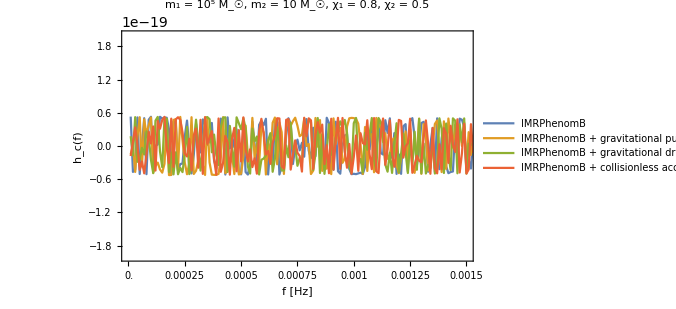

```mathematica
ListLinePlot[{hcfd,hcgravfd,hcdragfd,hccollessfd},FrameTicks->{{Automatic,None},{xticks,None}}, PlotRange->{{0,150},{-2*10^-19,2*10^-19}},ImageSize->500,Frame->True,Axes->False,FrameLabel->{{Style["h_c(f)",18],None},{Style["f [Hz]",18],None}},FrameStyle->Directive[14,GrayLevel[0],FontFamily->"CMU Serif",AbsoluteThickness[1]],PlotLegends->Placed[{Style["IMRPhenomB",Black,FontFamily->"CMU Sans Serif"],Style["IMRPhenomB + gravitational pull",Black,FontFamily->"CMU Sans Serif"],Style["IMRPhenomB + gravitational drag",Black,FontFamily->"CMU Sans Serif"],Style["IMRPhenomB + collisionless accretion",Black,FontFamily->"CMU Sans Serif"]},Scaled[{0.6,0.8}]],PlotLabel->Style["m_1 = 10^5 M_☉, m_2 = 10 M_☉, χ_1 = 0.8, χ_2 = 0.5",15,Black,FontFamily->"CMU Sans Serif",Italic]]
```

```mathematica
xlogticks=Table[{10^5 i,N[i]},{i,{10^-5,10^-4,10^-3,10^-2,10^-1,1}}]
```

{{1,0.00001},{10,0.0001},{100,0.001},{1000,0.01},{10000,0.1},{100000,1.}}

The next plot shows Maselli’s |h_n(f)|^2 and the waveforms’ |h_c(f)|^2 created earlier, plotted in a log-log scale. Compare with Kocsis et. al’s Figure 8 in Kocsis et. al (2011). https://doi.org/10.1103/PhysRevD.84.024032

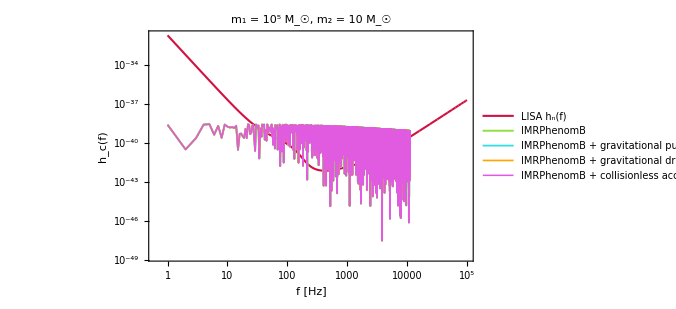

```mathematica
ListLogLogPlot[{(Abs[LISAhnf])^2,(Abs[hcfd])^2,(Abs[hcgravfd])^2,(Abs[hcdragfd])^2,(Abs[hccollessfd])^2},Joined->True,FrameTicks->{Automatic,{xlogticks,None}}, PlotRange->{Automatic,Automatic},ImageSize->500,Frame->True,Axes->False,FrameLabel->{{Style["h_c(f)",18],None},{Style["f [Hz]",18],None}},FrameStyle->Directive[14,GrayLevel[0],FontFamily->"CMU Serif",AbsoluteThickness[1]],GridLines->{{{11004,Directive[Black,Thick,Dashed]}}, None},PlotLegends->Placed[{Style["LISA h_n(f)",Black,FontFamily->"CMU Sans Serif"],Style["IMRPhenomB",Black,FontFamily->"CMU Sans Serif"],Style["IMRPhenomB + gravitational pull",Black,FontFamily->"CMU Sans Serif"],Style["IMRPhenomB + gravitational drag",Black,FontFamily->"CMU Sans Serif"],Style["IMRPhenomB + collisionless accretion",Black,FontFamily->"CMU Sans Serif"]},Scaled[{0.35,0.25}]],PlotStyle->{Directive[C2,AbsoluteThickness[1.5]],Directive[C7,AbsoluteThickness[1.4]],Directive[C5,AbsoluteThickness[1.3]],Directive[C4,AbsoluteThickness[1.2]],Directive[C9,AbsoluteThickness[1.1]]},ImagePadding->{{75,55},{75,10}},PlotLabel->Style["m_1 = 10^5 M_☉, m_2 = 10 M_☉",18,Black,FontFamily->"CMU Sans Serif"]]
```

```mathematica
𝒪[Noise_,h1_,h2_,fI_,fE_]:=4Re[NIntegrate[SetPrecision[h1*Conjugate[h2]
	/(Noise cc^2),40],{f,fI,fE},MaxRecursion->50,PrecisionGoal->25,AccuracyGoal->23,WorkingPrecision->30]];
```

```mathematica
SNR[𝒹_,m1_,m2_,χeff_,t_]:=Block[{ℳ,η,q=m1/m2,d,τ,ϕ,χ, 𝒽1,𝒽2,
	ρ,C,𝒫,i,j,fmin,fmax,f,IscoS,𝒯,𝒩,amp,M=m1+m2,h1},

Off[NIntegrate::slwcon];
Off[NIntegrate::eincr];

C=√5;

(* ---- Binary parameters q = m1/m2 ≥ 1 ---- *)
{ℳ,η,τ,ϕ,χ,d} = {(q/(1+q)^2)^(3/5)msun (M),q/(1+q)^2,0,-π/4,χeff,𝒹};
 
(* ---- Time of observation in terms of 4 months; 4 years = 12x 4 months = 48 months ---- *)
𝒯=t/3;

IscoS=cc 𝒻1[(M)msun,η,χ]+0cc/(π 6^(3/2)(M)msun); (* in Hz *)
amp[f_]=C (2/5)/(d 10^6 pc π^(2/3))(5/24)^(1/2) (f/cc)^(-7/6) ℳ^(5/6);
𝒽1[f_] =amp[f] hPhBppEVac[f/cc][ℳ,η,χ,τ,ϕ,d]; (* in km *)
(* 𝒽2[f_] =amp[f] hPhBppEVac[f/cc][ℳ,η,χ,τ,ϕ,d]*Exp[-I ψenv[f/cc]]; *)

fmin = Max[10^-5,4.149 10^-5 (ℳ/msun 10^-6)^(-5/8) 𝒯^(-3/8)];
fmax = Min[1,IscoS];

ρ = Sqrt[𝒪[LISA[f],𝒽1[f],𝒽1[f],fmin,fmax]];
h1[f_]=𝒽1[f]/ρ; (* f in km^-1 *)
(* Print["f_min = ",fmin," -- f_max = ", fmax]; *)
Return[ρ]
]
```

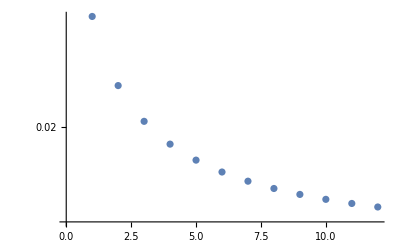

```mathematica
ListLogPlot[Table[SNR[1000, 10^5,10,(10^5*0.8+10*0.5)/(10^5+10),t],{t,1,12}]]
```

```mathematica
metric[dim_,𝒹_,m1_,m2_,χeff_,index_]:=Block[{ℳ,η,q=m1/m2,d,τ,ϕ,χ, ρ0,𝒽,d𝒽,
	ρ,C,𝒫,i,j,Γ,Σ,fmin,fmax,f,IscoS,𝒯=4,𝒩,amp},

Off[NIntegrate::slwcon];
Off[NIntegrate::eincr];

C=Sqrt[5];

(* ---- Creating the vacuum waveform from the input parameters ---- *)
(* ---- Binary parameters q = m1/m2 ≥ 1 ---- *)
{ℳ,η,τ,ϕ,χ,d} = {(q/(1+q)^2)^(3/5)msun (m1+m2),q/(1+q)^2,0,-π/4,χeff,𝒹};
 
(* ---- environmental correction ---- *)

ρ0  = 0;

IscoS=cc 𝒻1[(m1+m2)msun,η,χ]+0cc/(π 6^(3/2)(m1+m2)msun); (* PhenomB I-M transition freq *)
amp[f_]=C (2/5)/(d 10^6 pc π^(2/3))(5/24)^(1/2) (f/cc)^(-7/6) ℳ^(5/6); (* Constant amplitude, based only on Subscript[d, L] and chirp mass *)
𝒽[f_] =amp[f] hPhBppE[f/cc][ℳ,η,χ,τ,ϕ,d,ρ0,index];
(*d𝒽[f_] = amp[f]Table[deriv[[i]][f],{i,1,dim}]; *)

(* ---- Setting the limits of integration per detector ---- *)
fmin = Max[10^-5,4.149 10^-5 (ℳ/msun 10^-6)^(-5/8) 𝒯^(-3/8)];

fmax = Min[1,IscoS];

(* ---- Signal to noise ratio ---- *)

ρ = Sqrt[𝒪[LISA[f],𝒽[f],𝒽[f],fmin,fmax]];


d𝒽[f_] = (1/ρ^2)* amp[f]dhdθ[f/cc,index]; (* differentiated waveform; input for Fisher integral *)

Print["𝒞 = ",C," -- ℳ/M_⊙, = ",ℳ/msun,"-- η = ",N[η]," -- χ_eff = ",χ];

𝒩 = NIntegrate[f/cc^2/(96/(5π ℳ^2) (π ℳ f/cc)^(11/3)),{f,fmin,fmax}];

Print[" -- [\!\(\*SubscriptBox[\(f\), \(min\)]\),\!\(\*SubscriptBox[\(f\), \(max\)]\)] = [",fmin," , ",fmax,"]Hz -- ρ = ",NumberForm[ρ,6]," -- # cycles = ",𝒩];

(* ---- This a prior on the spin parameters |Subscript[χ, 1,2]|≤1 ---- *)

Γ = ConstantArray[0,{dim,dim}];

(* ---- Compute the Fisher and Covariance Matrix ---- *)

Monitor[For[i=1,i<=dim,i++,
	For[j=1,j<=i,j++,
		Γ[[i,j]] = If[i==j,𝒪[LISA[f],d𝒽[f][[i]],d𝒽[f][[j]],fmin,fmax],
								2𝒪[LISA[f],d𝒽[f][[i]],d𝒽[f][[j]],fmin,fmax]];
		]
	],
	Γ//MatrixForm];

Γ = Normal[Symmetrize[Γ]];

Print["Positive Matrix ? "PositiveDefiniteMatrixQ[Γ]];

Σ=If[PositiveDefiniteMatrixQ[Γ],LinearSolve[Γ,IdentityMatrix[dim],Method->"Cholesky"],Inverse[Γ]];

Return[{Γ,Σ}];

]
```

```mathematica
metric[6,1000,10^5,10,(10^5*0.8+10*0.5)/(10^5+10),-2]
```

𝒞 = √5 -- ℳ/M_⊙, = 398.099-- η = 0.00009998 -- χ_eff = 0.79997

-- [f_min,f_max] = [0.00328985 , 0.113325]Hz -- ρ = 64.3190 -- # cycles = 658378.

Positive Matrix ?  True

{{{4.01559518256144906646138188091×10^8,-3.5561121578376207915712497625×10^6,-0.0000294067220155278874638548604412,-260.816498213748438487800917033,-3.7216585339900499668131139604×10^7,-3.51814898293282618394294834045×10^18},{-3.5561121578376207915712497625×10^6,56386.193619455887172228155748,6.38550339189444895209772904543×10^-7,3.6363850914160391059757621686,394504.583854149123083897644626,2.28154077114288600773216804046×10^16},{-0.0000294067220155278874638548604412,6.38550339189444895209772904543×10^-7,1.18506211689889404761303358467×10^-17,4.16437430678016539074711040689×10^-11,3.57609391087543838768338016309×10^-6,172858.358339995553354716910791},{-260.816498213748438487800917033,3.6363850914160391059757621686,4.16437430678016539074711040689×10^-11,0.000241725106664869694687547229807,27.5295076908686282361910936739,1.87630827448562372014819660382×10^12},{-3.7216585339900499668131139604×10^7,394504.583854149123083897644626,3.57609391087543838768338016309×10^-6,27.5295076908686282361910936739,3.62607208031087924900073960537×10^6,3.01234497471649221679612478352×10^17},{-3.51814898293282618394294834045×10^18,2.28154077114288600773216804046×10^16,172858.358339995553354716910791,1.87630827448562372014819660382×10^12,3.01234497471649221679612478352×10^17,3.51427758257682001298231455697×10^28}},{{0.000386422049195761301332112158726,-0.0239895900005605050265072641897,-7.01042971977952278979883811547×10^7,289.054713357368923714869828397,0.00415601733568211198648240082295,3.54693625650703099902637752067×10^-15},{-0.0239895900005605050265072641897,1.5154627263462318869062976125,4.61527422724442853793187877961×10^9,-18486.2611836966940926734658917,-0.257587755571031302575948030456,-2.13198794264417237626711097714×10^-13},{-7.01042971977952278979883811547×10^7,4.61527422724442853793187877961×10^9,1.61762245481350187409530513287×10^19,-5.83633053445344455702478937358×10^13,-7.46110858833921219245904430734×10^8,-0.000582510568830390890234947346791},{289.054713357368923714869828397,-18486.2611836966940926734658917,-5.83633053445344455702478937358×10^13,2.27769239249660817057847503113×10^8,3097.24866470158858412893847917,2.5164279574900010869922504216×10^-9},{0.00415601733568211198648240082295,-0.257587755571031302575948030456,-7.46110858833921219245904430734×10^8,3097.24866470158858412893847917,0.0447298607791658574273233902463,3.81830650130927959391051956991×10^-14},{3.54693625650703099902637752067×10^-15,-2.13198794264417237626711097714×10^-13,-0.000582510568830390890234947346791,2.5164279574900010869922504216×10^-9,3.81830650130927959391051956991×10^-14,3.47413768579494666748178582661×10^-26}}}

```mathematica
%54//MatrixForm
```

((4.01559518256144906646138188091×10^8
-3.5561121578376207915712497625×10^6
-0.0000294067220155278874638548604412
-260.816498213748438487800917033
-3.7216585339900499668131139604×10^7
-3.51814898293282618394294834045×10^18) | (-3.5561121578376207915712497625×10^6
56386.193619455887172228155748
6.38550339189444895209772904543×10^-7
3.6363850914160391059757621686
394504.583854149123083897644626
2.28154077114288600773216804046×10^16) | (-0.0000294067220155278874638548604412
6.38550339189444895209772904543×10^-7
1.18506211689889404761303358467×10^-17
4.16437430678016539074711040689×10^-11
3.57609391087543838768338016309×10^-6
172858.358339995553354716910791) | (-260.816498213748438487800917033
3.6363850914160391059757621686
4.16437430678016539074711040689×10^-11
0.000241725106664869694687547229807
27.5295076908686282361910936739
1.87630827448562372014819660382×10^12) | (-3.7216585339900499668131139604×10^7
394504.583854149123083897644626
3.57609391087543838768338016309×10^-6
27.5295076908686282361910936739
3.62607208031087924900073960537×10^6
3.01234497471649221679612478352×10^17) | (-3.51814898293282618394294834045×10^18
2.28154077114288600773216804046×10^16
172858.358339995553354716910791
1.87630827448562372014819660382×10^12
3.01234497471649221679612478352×10^17
3.51427758257682001298231455697×10^28)
(0.000386422049195761301332112158726
-0.0239895900005605050265072641897
-7.01042971977952278979883811547×10^7
289.054713357368923714869828397
0.00415601733568211198648240082295
3.54693625650703099902637752067×10^-15) | (-0.0239895900005605050265072641897
1.5154627263462318869062976125
4.61527422724442853793187877961×10^9
-18486.2611836966940926734658917
-0.257587755571031302575948030456
-2.13198794264417237626711097714×10^-13) | (-7.01042971977952278979883811547×10^7
4.61527422724442853793187877961×10^9
1.61762245481350187409530513287×10^19
-5.83633053445344455702478937358×10^13
-7.46110858833921219245904430734×10^8
-0.000582510568830390890234947346791) | (289.054713357368923714869828397
-18486.2611836966940926734658917
-5.83633053445344455702478937358×10^13
2.27769239249660817057847503113×10^8
3097.24866470158858412893847917
2.5164279574900010869922504216×10^-9) | (0.00415601733568211198648240082295
-0.257587755571031302575948030456
-7.46110858833921219245904430734×10^8
3097.24866470158858412893847917
0.0447298607791658574273233902463
3.81830650130927959391051956991×10^-14) | (3.54693625650703099902637752067×10^-15
-2.13198794264417237626711097714×10^-13
-0.000582510568830390890234947346791
2.5164279574900010869922504216×10^-9
3.81830650130927959391051956991×10^-14
3.47413768579494666748178582661×10^-26))

```mathematica
errI[m1_,m2_,γ_,matrix_]:=With[{cc=2.998*10^8,G=6.67408 10^-11,M=(m1+m2)1.4768,Mc=(m1 m2)^(3/5)/(m1+m2)^(1/5)1.4768,ρH20=10^3},cc^2/G(Mc π)^-γ/(10^6 M^(2-γ))(Sqrt[Diagonal[matrix[[2]]]][[-1]])/ρH20]

errI2[m1_,m2_,γ_,matrix_,k0_]:=With[{cc=2.998*10^8,G=6.67408 10^-11,M=(m1+m2)1.4768,Mc=(m1 m2)^(3/5)/(m1+m2)^(1/5)1.4768,ρH20=10^3},cc^2/G(Mc π)^-γ/(10^6 M^(2-γ))(Sqrt[Diagonal[matrix[[2]]]][[-1]])/(ρH20 Abs[k0[m1,m2]])]
```

```mathematica
%54[[2]]
```

{{0.000386422049195761301332112158726,-0.0239895900005605050265072641897,-7.01042971977952278979883811547×10^7,289.054713357368923714869828397,0.00415601733568211198648240082295,3.54693625650703099902637752067×10^-15},{-0.0239895900005605050265072641897,1.5154627263462318869062976125,4.61527422724442853793187877961×10^9,-18486.2611836966940926734658917,-0.257587755571031302575948030456,-2.13198794264417237626711097714×10^-13},{-7.01042971977952278979883811547×10^7,4.61527422724442853793187877961×10^9,1.61762245481350187409530513287×10^19,-5.83633053445344455702478937358×10^13,-7.46110858833921219245904430734×10^8,-0.000582510568830390890234947346791},{289.054713357368923714869828397,-18486.2611836966940926734658917,-5.83633053445344455702478937358×10^13,2.27769239249660817057847503113×10^8,3097.24866470158858412893847917,2.5164279574900010869922504216×10^-9},{0.00415601733568211198648240082295,-0.257587755571031302575948030456,-7.46110858833921219245904430734×10^8,3097.24866470158858412893847917,0.0447298607791658574273233902463,3.81830650130927959391051956991×10^-14},{3.54693625650703099902637752067×10^-15,-2.13198794264417237626711097714×10^-13,-0.000582510568830390890234947346791,2.5164279574900010869922504216×10^-9,3.81830650130927959391051956991×10^-14,3.47413768579494666748178582661×10^-26}}

```mathematica
errI[10^5,10,2,%54]
```

0.0735817

```mathematica
Trial=Import["EMRIFisherpulllogm15.h5","Data"]
```

<|/Dataset1→{{{6.87237×10^15,-6.086×10^13,-503.272,-4.46366×10^9,-6.36932×10^14,-6.02103×10^24},{-6.086×10^13,9.65004×10^11,10.9283,6.22338×10^7,6.75163×10^12,3.90467×10^22},{-503.272,10.9283,2.02814×10^-10,0.000712699,61.202,2.95833×10^11},{-4.46366×10^9,6.22338×10^7,0.000712699,4136.93,4.71145×10^8,3.21115×10^18},{-6.36932×10^14,6.75163×10^12,61.202,4.71145×10^8,6.20573×10^13,5.15539×10^23},{-6.02103×10^24,3.90467×10^22,2.95833×10^11,3.21115×10^18,5.15539×10^23,6.0144×10^33}},{{2.2579×10^-11,-1.40174×10^-9,-4.09627,0.0000168898,2.4284×10^-10,2.07251×10^-21},{-1.40174×10^-9,8.855×10^-8,269.675,-0.00108017,-1.50511×10^-8,-1.24574×10^-19},{-4.09627,269.675,9.45193×10^11,-3.41023×10^6,-43.596,-3.40367×10^-10},{0.0000168898,-0.00108017,-3.41023×10^6,13.3088,0.000180975,1.47037×10^-15},{2.4284×10^-10,-1.50511×10^-8,-43.596,0.000180975,2.61361×10^-9,2.23108×10^-20},{2.07251×10^-21,-1.24574×10^-19,-3.40367×10^-10,1.47037×10^-15,2.23108×10^-20,2.02997×10^-31}}}|>

```mathematica
Trial[[1]]//MatrixForm
```

((6.87237×10^15
-6.086×10^13
-503.272
-4.46366×10^9
-6.36932×10^14
-6.02103×10^24) | (-6.086×10^13
9.65004×10^11
10.9283
6.22338×10^7
6.75163×10^12
3.90467×10^22) | (-503.272
10.9283
2.02814×10^-10
0.000712699
61.202
2.95833×10^11) | (-4.46366×10^9
6.22338×10^7
0.000712699
4136.93
4.71145×10^8
3.21115×10^18) | (-6.36932×10^14
6.75163×10^12
61.202
4.71145×10^8
6.20573×10^13
5.15539×10^23) | (-6.02103×10^24
3.90467×10^22
2.95833×10^11
3.21115×10^18
5.15539×10^23
6.0144×10^33)
(2.2579×10^-11
-1.40174×10^-9
-4.09627
0.0000168898
2.4284×10^-10
2.07251×10^-21) | (-1.40174×10^-9
8.855×10^-8
269.675
-0.00108017
-1.50511×10^-8
-1.24574×10^-19) | (-4.09627
269.675
9.45193×10^11
-3.41023×10^6
-43.596
-3.40367×10^-10) | (0.0000168898
-0.00108017
-3.41023×10^6
13.3088
0.000180975
1.47037×10^-15) | (2.4284×10^-10
-1.50511×10^-8
-43.596
0.000180975
2.61361×10^-9
2.23108×10^-20) | (2.07251×10^-21
-1.24574×10^-19
-3.40367×10^-10
1.47037×10^-15
2.23108×10^-20
2.02997×10^-31))